```mathematica
$MinPrecision=53;
```

```mathematica
(*Change precision as Brian said*)
```

### General Parameters

```mathematica
uoD=2;
Nx=50;
Ny=50;
Lx=10;
Ly=10;
uOuterMinPar=0.1;
uOuterMaxPar=1.1;
ui=12;
UoD=2;
uo=24;
AAA=0.7;
```

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_"<>"Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_"<>ToString[UoD]<>"uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_A"<>StringReplace[ToString[AAA],"."->"d"]<>"/BB_TC_"<>"Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_"<>ToString[UoD]<>"uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_A"<>StringReplace[ToString[AAA],"."->"d"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=uOuterMinPar;
uOuterMax= uOuterMaxPar;
uOuterDomains=UoD;
uOuterNodes=uo;
uInnerNodes=ui;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,0.6,1.1}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

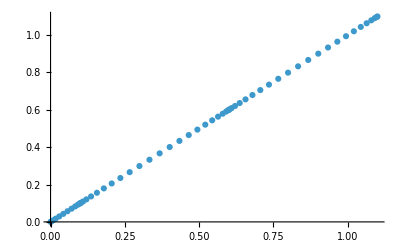

```mathematica
ListPlot[Transpose[{uValues,uValues}]]
```

#### x Domain

```mathematica
xMin=-Lx/2;
xMax=Lx/2;
xNodes=Nx;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-5,-24/5,-23/5,-22/5,-21/5,-4,-19/5,-18/5,-17/5,-16/5,-3,-14/5,-13/5,-12/5,-11/5,-2,-9/5,-8/5,-7/5,-6/5,-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5,4,21/5,22/5,23/5,24/5}

#### y Domain

```mathematica
yMin=-Ly/2;
yMax=Ly/2;
yNodes=Ny;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues
```

{-5,-24/5,-23/5,-22/5,-21/5,-4,-19/5,-18/5,-17/5,-16/5,-3,-14/5,-13/5,-12/5,-11/5,-2,-9/5,-8/5,-7/5,-6/5,-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5,4,21/5,22/5,23/5,24/5}

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{58,50,50,3}

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
rh^4==0.9 //Solve
```

{{rh→-0.974004},{rh→0.-0.974004 ⅈ},{rh→0.+0.974004 ⅈ},{rh→0.974004}}

```mathematica
b=1(*0.974004*);
```

The horizon (b) has to be shifted by the energy computed in the masterscalar notebook. also, the 20 squared factor comes from the normalization factor used some paragraphs down.

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ//N
```

Function[{ρ,x,y},Hypergeometric2F1[-0.333333,0.5,0.666667,ρ^3 (-1. u1d[x,y]^2-1. u2d[x,y]^2)]/ρ+C[1][x,y]]

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u^2 a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp(*/.ξ->Function[{t,z,y},0]*)//Series[#,{u,0,2}]&
```

1/u^2+(2 ξ[t,x,y])/u+(ξ[t,x,y]^2-2 ξ^(1,0,0)[t,x,y])+a3[t,0,x,y] u^2+O[u]^3

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=u^-2(1-(b u)^4)//Simplify
```

1/u^2-u^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/u]==Coefficient[AToMatch,1/u],  C[1][x,y]]//Flatten
```

{}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
Coefficient[AToMatch,u^2]
```

-1

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,u^2]==Coefficient[AExpOfρ,u^2],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-1}

From Chasler paper a3 should be

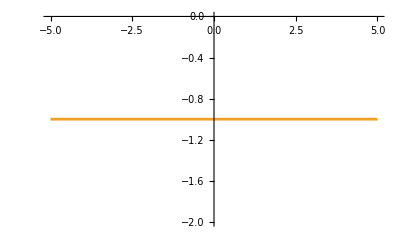

```mathematica
Plot[{-1/2(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,-5,5}]
```

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
a3Data[[13,1]]
```

-1

```mathematica
xiData=Table[(ξ[t,x,y]/.ξ[t,x,y]->0/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessData=Table[b,{i,1,xValues//Length},{j,1,yValues//Length}];
```

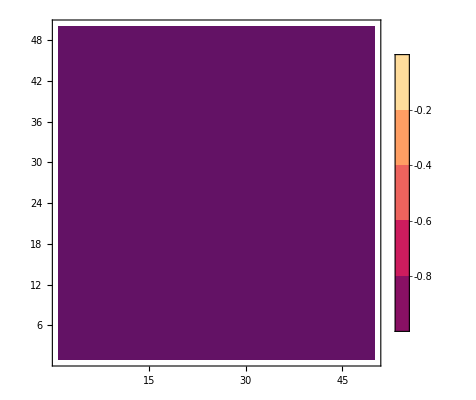

```mathematica
ListContourPlot[a3Data,PlotLegends->Automatic]
```

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7Initiala3_BBB.h5

```mathematica
Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7Initialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7Initialguess_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

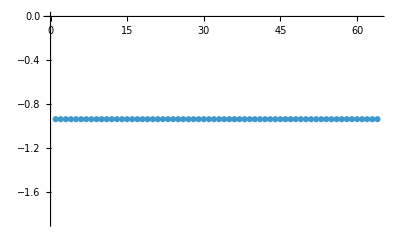

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"][[1,1]]]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u^2 f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&
```

ξ^(0,1,0)[t,x,y]+1. f1[t,z,y] ρ^2-2. (f1[t,z,y] C[1][x,y]) ρ^3+3. f1[t,z,y] (C[1][x,y])^2 ρ^4+O[ρ]^5

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
FToMatch=0;
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ^2]==Coefficient[FExpOfρ,ρ^2],f1[t,z,y]]//Simplify
```

{{f1[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

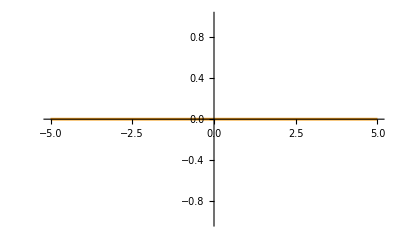

```mathematica
Plot[{-u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fxData=Table[((f1[t,z,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]]),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fxData//Dimensions
```

{50,50}

```mathematica
ListPlot3D[fxData]
```

-Graphics3D-

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7Initialfx_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u^2 f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=0;
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ^2]==Coefficient[F2ExpOfρ,ρ^2],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

-Graphics-

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyData=Table[(f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{50,50}

```mathematica
ListPlot3D[fyData]
```

-Graphics3D-

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},ρs]
```

Function[{ρs,xs,ys},ρs]

Horizon location

```mathematica
Minimize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
Maximize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
```

1

1

```mathematica
Plot3D[uofρ[b^-1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,(*PlotRange->All,*)(*MaxRecursion->4,*)ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

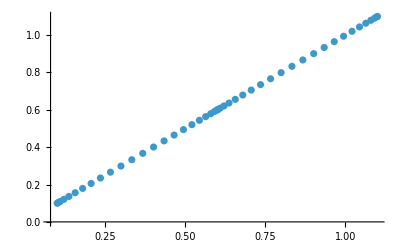

```mathematica
ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
```

{58,50,50,3}

```mathematica
ρofuValues=ParallelTable[u,{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{79.704,Null}

```mathematica
u1Values=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.000068,Null}

```mathematica
u2Values=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.000074,Null}

```mathematica
u0Values=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.000133,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=0;
```

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1]],0}]//Normal](*(1+ (RandomReal[]-0.5)/100)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.889374,Null}

```mathematica
InitialB=ParallelTable[0,{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

{74.1189,Null}

```mathematica
InitialB//Dimensions
```

{58,50,50}

```mathematica
ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000073,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000364,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7InitialB_BBB.h5

#### B2 Function

ExpOfHxy=Exp[-ⅈ ω (t- Integrate[1/f[z],z])]

{ϕvev→-15.79580470746918506167762437545892886598578928681675346-44.79911603541786660966127959632532578392261857116266207 ⅈ,ω→-5.169520975762229549404618858897224991945721855354884116-4.763570116920460863645146483709052189501385495221501904 ⅈ}

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt))/.ω->-5.16952097576222954940461885889722499194572185535488411636773071714438971882811`55.-4.76357011692046086364514648370905218950138549522150190381951475957642922361821`55. ⅈ;
```

```mathematica
NormFactor=Maximize[ u^2 Abs[ 2 InterpolatingFunction[…][u] ],u>=0&&u<=1,u][[1]];
Parametricgxy[u_]:=AAA(*0.1Exp[(-(u-0.8)^2)/0.1^2]*) (*0.37909844692106875*) u^2((2  InterpolatingFunction[…][u] )/NormFactor//Re);
```

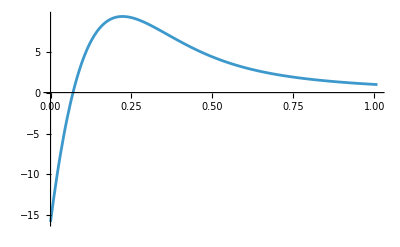

```mathematica
Plot[{InterpolatingFunction[…][u]//Re},{u,0,1.01},PlotRange->All]
```

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==(*2^-1*)(*u^-2*)a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}](*[[1]]*)/. C[1]->0/. C[2]->0/.C[3]->0
```

{{S→-((1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(1-a^2 u^4)^(1/6)]/u^4},{S→-((1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-a^2 u^4)^(1/6)]/u^4},{S→-((1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-a^2 u^4)^(1/6)]/u^4},{S→-((1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(1-a^2 u^4)^(1/6)]/u^4},{S→((1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(1-a^2 u^4)^(1/6)]/u^4},{S→((1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-a^2 u^4)^(1/6)]/u^4},{S→((1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-a^2 u^4)^(1/6)]/u^4},{S→((1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(1/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(-√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4},{S→((-1)^(2/3) (1-a^2 u^4)^(1/6))/u,Gin→Log[(√(1-a^2 u^4)+a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-a^2 u^4)^(1/6)]/u^4}}

```mathematica
{S->-((4-a^2)^(1/6))/(2^(1/3) u),Gin->Log[(-2 √(4-a^2)-a √(4-a^2))/(-4+a^2)]/u^4,B1in->0,B2in->-Log[((4-a^2)^(1/6))/2^(1/3)]/u^4}
```

{S→-((4-a^2)^(1/6))/(2^(1/3) u),Gin→Log[(-2 √(4-a^2)-a √(4-a^2))/(-4+a^2)]/u^4,B1in→0,B2in→-Log[((4-a^2)^(1/6))/2^(1/3)]/u^4}

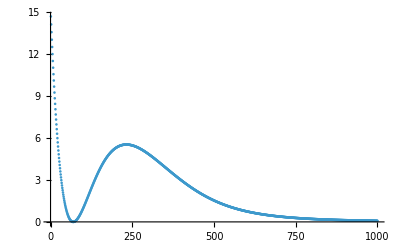

```mathematica
ListPlot[ParallelTable[N[-Log[ (1-a^2)^(1/6)]/u^4/.a->Parametricgxy[ui]/.u->ui],{ui,0.001,1,0.001}],PlotRange->All]
```

```mathematica
InitialB2=ParallelTable[N[-Log[ (1-a^2)^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {1.02064} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Input value `1` lies outside the range of data in the interpolating function. Extrapolation will be used. will be suppressed during this calculation.

{516.466,Null}

```mathematica
InitialB2//Im//Abs//Flatten//Norm
```

0

```mathematica
Series[-Log[(1-a^2 u^4)^(1/6)]/u^4/.a->aa u^2,{u,0,8}](*/.u->0*)
```

11.2368 u^4+O[u]^9

```mathematica
Series[Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4/.a->aa u^2,{u,0,8}](*/.u->0*)
```

-8.21102-184.532 u^8+O[u]^9

```mathematica
Series[-((1-a^2 u^4)^(1/6))/u/.a->aa u^2,{u,0,8}]
```

-1/u+11.2368 u^7+O[u]^9

```mathematica
InitialB2uzero=ParallelTable[0,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.821757,Null}

```mathematica
InitialB2[[1]]=InitialB2uzero;
```

```mathematica
ExportDataB2=Join[{InitialB2(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB2(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000127,Null}

```mathematica
ExportAttributesB2=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataB2=Table[ExportAttributesB2[[i]]->ExportDataB2[[i]],{i,1,ExportAttributesB2//Length}];//AbsoluteTiming
```

{0.002186,Null}

```mathematica
Export[IDFolderName<>"InitialB2_BBB.h5",AttributesAndDataB2,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7InitialB2_BBB.h5

#### G Function

```mathematica
uValues[[2]]
```

0.00202535

```mathematica
Series[Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4/.a->aa u^2,{u,0,8}](*/.u->0*)
```

-8.21102-184.532 u^8+O[u]^9

```mathematica
(*This has to be taken from the notebook TensorChannelAIMEdata, related to the vev, Eout and the rescaling*)
```

```mathematica
(Parametricgxy[u] u^-2//Simplify)/.u->0
```

-9.57953

```mathematica
aa=(Parametricgxy[u] u^-2//Simplify)/.u->0;
```

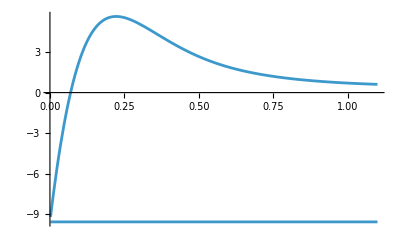

```mathematica
Plot[{aa,Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4}/.a->Parametricgxy[u],{u,uValues[[2]],1.1},PlotRange->All]
```

```mathematica
InitialG=ParallelTable[N[Log[(-√(1-a^2 u^4)-a u^2 √(1-a^2 u^4))/(-1+a^2 u^4)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision]//Re,{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {1.02064} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Input value `1` lies outside the range of data in the interpolating function. Extrapolation will be used. will be suppressed during this calculation.

{493.052,Null}

```mathematica
InitialG1=ParallelTable[aa,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.867399,Null}

```mathematica
InitialG[[1]]=InitialG1;
```

```mathematica
InitialG//Dimensions
```

{58,50,50}

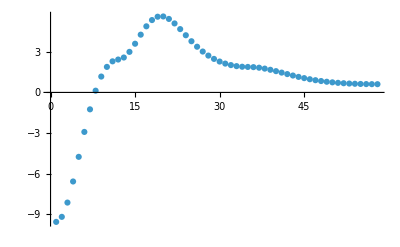

```mathematica
ListPlot[InitialG[[;;,1,1]],PlotRange->All]
```

```mathematica
ExportDataG=Join[{InitialG(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialG(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000092,Null}

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->ExportDataG[[i]],{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.001456,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7/BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d7InitialG_BBB.h5

#### ϕ Function

```mathematica
(*Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialphi_BB.h5",AttributesAndData,"Datasets"]*)
```

```mathematica
testImport=Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"]
```

```mathematica
dd
```

dd

```mathematica
8
```

8

## BM

```mathematica
Solve[{S^2 E^-B1 Cosh[G]==u^-2,S^2 E^B1 Cosh[G]==u^-2,S^2 2 Sinh[G]==a},{S,G,B1}]/. C[1]->0/. C[2]->0
```

{{S→-((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→-((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→-(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→-(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π},{S→(ⅈ (4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)+a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(-2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→0},{S→((4-a^2 u^4)^(1/4))/(√2 u),G→Log[(2 √(4-a^2 u^4)-a u^2 √(4-a^2 u^4))/(-4+a^2 u^4)],B1→-ⅈ π}}